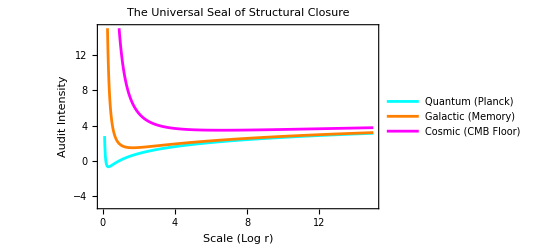

```mathematica
(*The Universal Seal:Multi-Scale Grover Audit*)R=1.15428;
scales={0.05,1.0,10.0}; (*Planck,Galactic,Cosmic Proxy*)
GroverPotential[r_,s_]:=(s/r^2)+R*Log[r+s];

Plot[Evaluate[Table[GroverPotential[r,s],{s,scales}]],{r,0.1,15},PlotStyle->{Cyan,Orange,Magenta},PlotRange->{-5,15},Frame->True,FrameLabel->{"Scale (Log r)","Audit Intensity"},PlotLegends->{"Quantum (Planck)","Galactic (Memory)","Cosmic (CMB Floor)"},PlotLabel->"The Universal Seal of Structural Closure"]
```